```mathematica
ClearAll["Global`*"]
w=0.7;
period=2*Pi/w;
A=1;
tmax=1000;
soln=ParametricNDSolve[{theta''[t]+(1/Q) * theta'[t]+Sin[theta[t]]==A  Cos[w t],theta[0]==0,theta'[0]==0},theta,{t,0,tmax},{Q}];
```

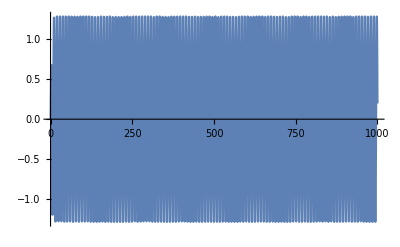

```mathematica
Q=1;
Plot[theta[Q][x]/.soln,{x,0,tmax}]
```

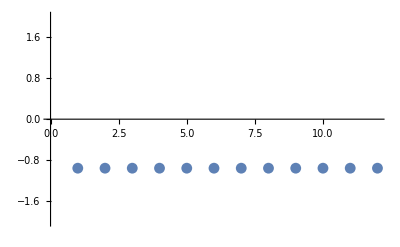

```mathematica
(*generate bifurcation plot*)
tdel=period;
result=Flatten[Table[theta[Q][x]/.soln,{x,400,500,tdel}]];
ListPlot[result,PlotRange->{All,{-2,2}}]
```

```mathematica
tdel=period;
For[i=1,i<14,i++,
results=Flatten[Table[theta[i/20][x]/.soln,{x,400,500,tdel}]];
bifur[[i]]=Transpose[{ConstantArray[i,Length[results]],results}];

]
```

Set::partw: Part 13 of {{{1, -0.0300564}, {1, -0.0300564}, {1, -0.0300564}, « 6 », {1, -0.0300564}, {1, -0.0300564}, {1, -0.0300564}}, « 11 »} does not exist.

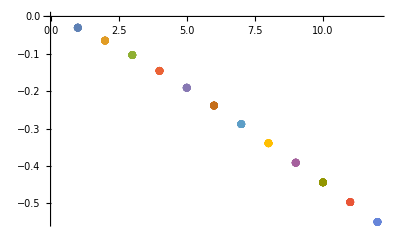

```mathematica
ListPlot[bifur]
```

```mathematica
results=Flatten[Table[theta[i/20][x]/.soln,{x,400,500,tdel}]];
bifur[[i]]=Transpose[{ConstantArray[i,Length[results]],results}];
```